```mathematica
DSolve[y'[x]/y[x]==-(3/2)*(Sin[2x]/Cos[2x]),y[x],x]
```

{{y[x]→C[1] Cos[2 x]^(3/4)}}

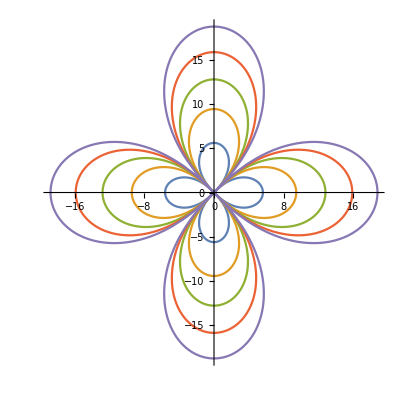

```mathematica
g1=PolarPlot[Evaluate[Table[Power[Abs[k*Cos[2 t]],3/4],{k,10,50,10}]],{t,0,2 Pi},DisplayFunction->Identity];
Show[g1,DisplayFunction->$DisplayFunction]
```